## Tables for t and U, calculated in bandstructure_03.nb

```mathematica
tTable={{1.,0.17811760405711083},{2.,0.14275501566376778},{3.,0.11102731758147985},{4.,0.08549007052155906},{5.,0.06576734588078084},{6.,0.05077302742621848},{7.,0.03941717252357294},{8.,0.03079925633549434},{9.,0.024226709022146336},{10.,0.019182452160096508},{11.,0.015284694581656946},{12.,0.012252083019890241},{13.,0.009876707580435753},{14.,0.008004101806064867},{15.,0.006518815773354448},{16.,0.0053339159146984765},{17.,0.0043834992368303426},{18.,0.003617253423980414},{19.,0.002996508800804228},{20.,0.0024913513569176948},{21.,0.0020784971715070355},{22.,0.0017397164661691216},{23.,0.0014606570206704894},{24.,0.0012299597666029294},{25.,0.0010385896218309543},{26.,0.0008793259696823438},{27.,0.0007463723512085041},{28.,0.0006350557293833355},{29.,0.0005415942382596435},{30.,0.00046291403663189},{31.,0.0003965059781266607},{32.,0.0003403217883794957},{33.,0.00029267575592688375},{34.,0.0002521803144467349},{35.,0.0002176890339151899},{36.,0.00018825200305553252},{37.,0.00016307988896463932},{38.,0.00014151502765706323},{39.,0.00012300822005816098},{40.,0.00010709954850028485}};
t=Interpolation[tTable];
```

### Comparisson between exact t and t from Mathieu (valid for strong lattices)

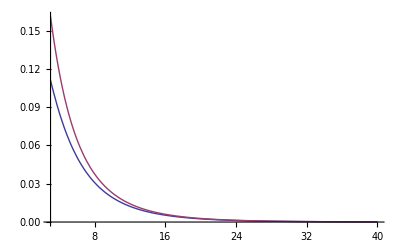

```mathematica
tMathieu[v0_]:=4/(√π)v0^(3/4)Exp[-2 √v0];
Plot[{Re[t[v0]],tMathieu[v0]},{v0,3,40},PlotRange->All]
```

```mathematica
uTable={{1.,2.3489551946979854},{2.,4.174809192881718},{3.,6.257612977452876},{4.,8.47774647686555},{5.,10.73940269474932},{6.,12.985311104810195},{7.,15.187735921975193},{8.,17.33649814732915},{9.,19.430374541390133},{10.,21.47212383790033},{11.,23.465933315886126},{12.,25.416221371959296},{13.,27.327132710705303},{14.,29.202365235704395},{15.,31.04514573679708},{16.,32.858265938101916},{17.,34.644137972232095},{18.,36.40485142134472},{19.,38.14222494322565},{20.,39.85785043841656},{21.,41.5531298192331},{22.,43.22930522875123},{23.,44.887483755635024},{24.,46.528657643433824},{25.,48.15372085940882},{26.,49.76348273802645},{27.,51.35867927609209},{28.,52.939982539072346},{29.,54.508008543134686},{30.,56.063323900804676},{31.,57.606451458608085},{32.,59.13787510803696},{33.,60.65804391452455},{34.,62.167375680432336},{35.,63.66626003554756},{36.,65.15506113087405},{37.,66.63411999749435},{38.,68.10375662113215},{39.,69.56427177420291},{40.,71.01594863991863}};
uWannierFactor=Interpolation[uTable];
```

### The interpolation functions are saved to a dat file, so that they can be used in the display physics program

```mathematica
Module[{head,stream,dat},
dat=Table[{v0, t[v0],uWannierFactor[v0]},{v0,1.,40.,0.1}];
SetDirectory[NotebookDirectory[]];
head="#v0\tt(Er)\tuWannierFactor(Er/latticeSpacing)\n";
stream=OpenWrite["tANDU.dat"];
WriteString[stream,head<>ExportString[dat,"Table"]];
Close[stream];]
```

### U as a function of magnetic field: The scattering length is obtained using the formula from Innsbruck

bohr radius = 5 e-11
lattice spacing = 5 e-7
need 10,000 a0 to get scattering length equal to the lattice spacing

```mathematica
a12[B_]:=Module[{ab=-1405.,b0=834.149,d=300.,α=0.00040,aInBohrRadii,bohrRadius,latticeSpacing,aInLattSpacing},
aInBohrRadii=ab(1+d/(B-b0))(1+α(B-b0));
bohrRadius=5.29 10^-11;
latticeSpacing=(1.064 10^-6)/2;
aInLattSpacing=aInBohrRadii bohrRadius/latticeSpacing;
aInLattSpacing]
```

### And the formula for U in units of Er is below

```mathematica
uBfield[v0_,B_]:=a12[B]uWannierFactor[v0]
```

### Also the formula for U as a function of the scattering length is given below

```mathematica
u[v0_,as_]:=Module[{bohrRadius=5.29 10^-11,latticeSpacing=0.532 10^-6,aInLattSpacing},
aInLattSpacing=as bohrRadius/latticeSpacing;
aInLattSpacing uWannierFactor[v0]]
```

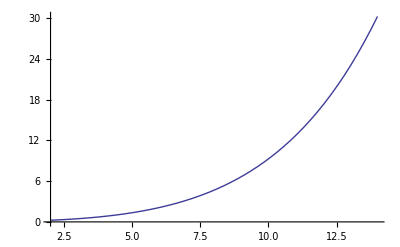

```mathematica
Plot[uBfield[v0,664.06]/(12 t[v0]),{v0,2,14.}]
```

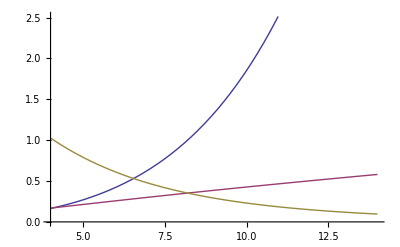

```mathematica
Plot[{u[v0,200]/(12 t[v0]), u[v0,200], 12t[v0]},{v0,4.,14.}]
```

```mathematica
u[v0,200]/(12 t[v0])/.{v0->10}
```

1.85508

```mathematica
fns[v0_]:=Table[u[v0,as]/(12 t[v0]),{as,{100,200,600,1000}}];
len:=Length[fns[x]];
g1=DynamicModule[{pos=Table[{4.,fns[4.][[i]]},{i,len}]},
LocatorPane[Dynamic[pos],LogPlot[Evaluate[fns[v0]],{v0,4,14.},PlotStyle->{Thickness[0.01]},GridLines->Automatic,Frame->True,FrameLabel->{"V0/E_R","U/12t"},LabelStyle->Directive[FontFamily->"Times",FontSize->18,Bold],ImageSize->{600}],Appearance->Table[Framed[Text@TraditionalForm[as"a_0"],RoundingRadius->5,Background->White],{as,{100,200,600,1000}}]]]
```

```mathematica
g1
```

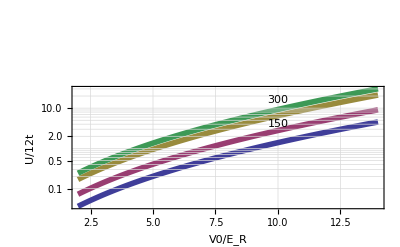

```mathematica
funs[v0_]:=Table[u[v0,as]/(12 t[v0]),{as,{150,300,700,1000}}]
LogPlot[Evaluate[funs[v0]],{v0,2,14.},PlotStyle->{Thickness[0.01]},GridLines->Automatic,Frame->True,FrameLabel->{"V0/E_R","U/12t"},LabelStyle->Directive[FontFamily->"Times",FontSize->18,Bold],ImageSize->{400},Epilog->Table[Inset[Framed[DisplayForm[as],RoundingRadius->5],{10,u[10.,as]/(12 t[10.])},Background->White],{as,{150,300,700,1000}}]]
```

```mathematica
Table[Inset[Framed[DisplayForm[as],RoundingRadius->5],{10,u[10.,as]/(12 t[10.])},Background->White],{as,{150,300,700,1000}}]
```

{Inset[150,{10,1.39131},Background→GrayLevel[1]],Inset[300,{10,2.78263},Background→GrayLevel[1]],Inset[700,{10,6.4928},Background→GrayLevel[1]],Inset[1000,{10,9.27542},Background→GrayLevel[1]]}